```mathematica
ta = {0.1,0.05,1.4,1.5,2,2.05,3.4,3.5};
tb = {1,-1.5,1.75,-0.75,6,5,0.01,-1.75};
Выбираем степень полинома;
m=8;
S=Array[s,{m,m}];
n=Length[ta];
X=Table[Sum[ta[[i]]^j/n,{i,n}],{j,0,2*(m-1)}]
```

{1.,1.75,4.52938,13.1143,40.7827,132.594,442.526,1499.26,5123.12,17592.9,60589.2,209030.,721929.,2.49511×10^6,8.6278×10^6}

```mathematica
TA=Table[s[i,j]=X[[i+j-1]],{i,m},{j,m}];
TableForm[TA]
```

1. | 1.75 | 4.52938 | 13.1143 | 40.7827 | 132.594 | 442.526 | 1499.26
1.75 | 4.52938 | 13.1143 | 40.7827 | 132.594 | 442.526 | 1499.26 | 5123.12
4.52938 | 13.1143 | 40.7827 | 132.594 | 442.526 | 1499.26 | 5123.12 | 17592.9
13.1143 | 40.7827 | 132.594 | 442.526 | 1499.26 | 5123.12 | 17592.9 | 60589.2
40.7827 | 132.594 | 442.526 | 1499.26 | 5123.12 | 17592.9 | 60589.2 | 209030.
132.594 | 442.526 | 1499.26 | 5123.12 | 17592.9 | 60589.2 | 209030. | 721929.
442.526 | 1499.26 | 5123.12 | 17592.9 | 60589.2 | 209030. | 721929. | 2.49511×10^6
1499.26 | 5123.12 | 17592.9 | 60589.2 | 209030. | 721929. | 2.49511×10^6 | 8.6278×10^6

```mathematica
b=Table[Sum[ta[[i]]^j*tb[[i]]/n,{i,n}],{j,0,(m-1)}]
```

{1.22,2.18863,3.17992,2.33862,-9.25525,-67.2309,-305.223,-1209.06}

```mathematica
A=Inverse[TA].b
```

Inverse::luc: Result for Inverse of badly conditioned matrix {{1.,1.75,4.52938,13.1143,40.7827,132.594,442.526,1499.26},{1.75,4.52938,13.1143,40.7827,132.594,442.526,1499.26,5123.12},«5»,{1499.26,5123.12,17592.9,60589.2,209030.,721929.,2.49511×10^6,8.6278×10^6}} may contain significant numerical errors.

{2.63374,-165.474,1835.84,-3756.6,3254.98,-1398.14,293.293,-23.9544}

```mathematica
p[x_]:=Sum[A[[i]]*x^(i-1),{i,m}];
p[x]
```

2.63374-165.474 x+1835.84 x^2-3756.6 x^3+3254.98 x^4-1398.14 x^5+293.293 x^6-23.9544 x^7

```mathematica
TT=Transpose[{ta,tb}]
```

{{0.1,1},{0.05,-1.5},{1.4,1.75},{1.5,-0.75},{2,6},{2.05,5},{3.4,0.01},{3.5,-1.75}}

```mathematica
Среднеквадратическое отклонение определяется следующим образом;
Is=∑_(i=1)^n (p[TT[[i,1]]]-TT[[i,2]])^2/n
```

1.5221×10^-9

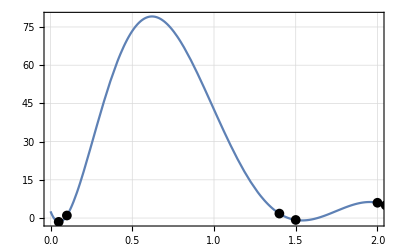

```mathematica
Рисуем графики;
plot=Plot[p[x],{x,0,2},Frame->True,GridLines->Automatic];
p2=ListPlot[TT,PlotStyle->Black,PlotMarkers->{Automatic,Medium}];
Show[plot,p2]
```

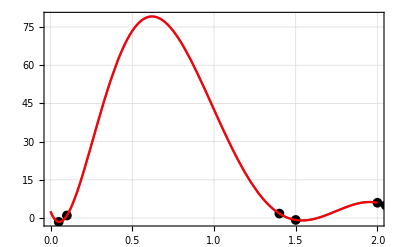

```mathematica
Рисуем многочлен при помощи функции Fit;
fit=Fit[TT,{1,x, x^2,x^3,x^4,x^5,x^6,x^7},x];
plotFit=Plot[fit,{x,0,2},Frame->True,GridLines->Automatic, PlotStyle->Red];
Show[plot,p2, plotFit]
```